```mathematica
(*s=InputString["Enter xml file name","tooth.xml"]//StringReplace[#," "->""]&;*)
xml=Import[NotebookDirectory[]<>"~images\\"<>"vorts1_optimized_parallelsearch.xml"];
{tfifile,volumefile,legends,face,imagefilenames,featurefilename,resultxml,imagefile,dataname,plotpath,imagepath}=xml;
Column[xml,Background->{{Lighter@LightYellow,Lighter@LightBlue}},Frame->True,FrameStyle->Directive[LightGray,Thin,Dashed]]
```

C:\work\time-varying-visualization\~plot\vorts1_optimized_parallelsearch.tfi
C:\_time_varying_data\vortex_tiff\vorts1.tif
{Feature 1,Feature 2,Feature 3,Feature 4,Feature 5}
top
{C:\work\time-varying-visualization\~images\vorts1_optimized_parallelsearch_saliency_chart.pdf,C:\work\time-varying-visualization\~images\vorts1_optimized_parallelsearch_visibility_chart.pdf,C:\work\time-varying-visualization\~images\vorts1_optimized_parallelsearch_visibility_saliency_brightness_chart.pdf,C:\work\time-varying-visualization\~images\vorts1_optimized_parallelsearch_visibility_saliency_saturation_chart.pdf,C:\work\time-varying-visualization\~images\vorts1_optimized_parallelsearch_visibility_saliency_weighted_chart.pdf}
C:\work\time-varying-visualization\~images\vorts1_optimized_parallelsearch_visibility_saliency_feature.png
C:\work\time-varying-visualization\~images\saliency.xml
C:\work\time-varying-visualization\~images\vorts1_optimized_parallelsearch.png
vorts1_optimized_parallelsearch
C:\work\time-varying-visualization\~plot\
C:\work\time-varying-visualization\~images\

```mathematica
tf=Import[tfifile,"XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;
```

```mathematica
d = Import[volumefile,"Image3D"];
colorized=Image3D[d,ColorFunction->rgbafunction];
{lightness,chroma,hue,opacity}=ImageApply[List@@rgbafunction[#]&,d]//Image3D[#,ColorSpace->"RGB"]&//ColorSeparate[ColorConvert[#,"LCH"]]&;
(*lo=ImageMultiply[lightness,opacity];
co=ImageMultiply[chroma,opacity];*)
(*g1=ImageDifference[GaussianFilter[lightness,{2,Sqrt[2]/8.*2}],GaussianFilter[lightness,{4,Sqrt[2]/8.*4}]]
g2=ImageDifference[GaussianFilter[chroma,{2,Sqrt[2]/8.*2}],GaussianFilter[chroma,{4,Sqrt[2]/8.*4}]]
g3=ImageDifference[GaussianFilter[hue,{2,Sqrt[2]/8.*2}],GaussianFilter[hue,{4,Sqrt[2]/8.*4}]];
g4=ImageDifference[GaussianFilter[opacity,{2,Sqrt[2]/8.*2}],GaussianFilter[opacity,{4,Sqrt[2]/8.*4}]];*)
{g1,g2,g3}=ParallelMap[ImageDifference[GaussianFilter[#,{2,Sqrt[2]/8.*2}],GaussianFilter[#,{4,Sqrt[2]/8.*4}]]&,{lightness,chroma,opacity}];

pos=intensity[[#]]&/@Flatten@Position[alpha,_?(#==0&)];
index=Flatten@Position[alpha,_?(#>0&)];
features=Table[ImageApply[If[#≥pos[[i]] && #≤pos[[i+1]],1,0]&,d],{i,1,Length[pos],2}];
chartcolors=rgbcolors[[#]]&/@index;
colorizedfeatures=ImageMultiply[colorized,#]&/@features;
viewpoints=<|"top":>Top,"back":>Back,"left":>Left,"bottom":>Bottom,"front":>Front,"right":>Right|>;
MapIndexed[Export[StringReplace[imagefile,"."->"_"<>ToString[First[#2]]<>"."],Show[#,Boxed->False,ViewPoint->viewpoints[face]]]&,colorizedfeatures];
Export[imagefile,Image3D[d,ColorFunction->rgbafunction,ViewPoint->viewpoints[face]]];

intensity0=intensity;
alpha0=alpha;
rangeOfAlpha=Range[Length[alpha]];
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0];rangeOfAlpha+=1];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];
(*ListLinePlot[Transpose[{intensity0,alpha0}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
fun=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];
(*Plot[fun[x],{x,0,1},PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
(*index0=Flatten@Position[alpha0,_?(#>0&)];*)
index0=Flatten@Position[alpha0,_?(#>0&)];
legends=MapIndexed["feature"<>ToString@First@#2&,index];
```

```mathematica
top3[fun_,volume_]:=Module[{list,img,list2,list3,df,d1},(* top *)
df=ImageApply[fun[#]&,volume];
list=Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d1=Image3D[list3]
]
back3[fun_,volume_]:=Module[{list,img,list2,list3,tmp,df,d2},(* back *)
df=ImageApply[fun[#]&,volume];
list=Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left3[fun_,volume_]:=Module[{list,img,list2,list3,tmp,df,d3},(* left *)
df=ImageApply[fun[#]&,volume];
list=Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom3[fun_,volume_]:=Module[{list,img,list2,list3,df,d4},(* bottom *)
df=ImageApply[fun[#]&,volume];
list=Reverse@Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d4=Image3D[Reverse[list3]]]
front3[fun_,volume_]:=Module[{list,img,list2,list3,tmp,df,d5},(* front *)
df=ImageApply[fun[#]&,volume];
list=Reverse@Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right3[fun_,volume_]:=Module[{list,img,list2,list3,tmp,df,d6},(* right *)
df=ImageApply[fun[#]&,volume];
list=Reverse@Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices3=<|"top":>top3,"back":>back3,"left":>left3,"bottom":>bottom3,"front":>front3,"right":>right3|>;
```

```mathematica
VisibilitySaliency[peaks_,data_]:=Module[{alpha2,fun,vis,viss,vs,mean,total},
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=renderslices3[face][fun,data];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
Visibility[fun_,data_]:=Module[{vis,viss,vs,mean,total},
vis=renderslices3[face][fun,data];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
VisibilityField[fun_,data_]:=Module[{vis},
vis=renderslices3[face][fun,data]
]
```

```mathematica
vpath=FileNameDrop[volumefile,-1];
vnames=Table["vorts"<>ToString[i]<>".tif",{i,99}];
vortexfilenames=FileNameJoin[{vpath,#}]&/@vnames;
vortices=Import[#,"Image3D"]&/@vortexfilenames;
```

```mathematica
SaliencyField[d_]:=Module[{colorized,lightness,chroma,hue,opacity,g1,g2,g3},
colorized=Image3D[d,ColorFunction->rgbafunction];
{lightness,chroma,hue,opacity}=ImageApply[List@@rgbafunction[#]&,d]//Image3D[#,ColorSpace->"RGB"]&//ColorSeparate[ColorConvert[#,"LCH"]]&;
{g1,g2,g3}=Map[ImageDifference[GaussianFilter[#,{2,Sqrt[2]/8.*2}],GaussianFilter[#,{4,Sqrt[2]/8.*4}]]&,{lightness,chroma,opacity}];
ImageMultiply[ImageAdd[g1,g2],0.5]
]
SaliencyField3[d_]:=Module[{colorized,lightness,chroma,hue,opacity,g1,g2,g3},
colorized=Image3D[d,ColorFunction->rgbafunction];
{lightness,chroma,hue,opacity}=ImageApply[List@@rgbafunction[#]&,d]//Image3D[#,ColorSpace->"RGB"]&//ColorSeparate[ColorConvert[#,"LCH"]]&;
{g1,g2,g3}=Map[ImageDifference[GaussianFilter[#,{2,Sqrt[2]/8.*2}],GaussianFilter[#,{4,Sqrt[2]/8.*4}]]&,{lightness,chroma,opacity}];
ImageMultiply[ImageAdd[g1,g2,g3],1/3.]
]
```

```mathematica
Vortex[vortices_,range_,index_]:=vortices[[range[[index]]]]
```

```mathematica
CloseKernels[];
LaunchKernels[];
```

```mathematica
path=NotebookDirectory[]<>"~spatiotemporal\\";
parts=Append[Range[5,93,11],24] (* frame 24 is invalid, frame 5,16,27,38,49,60,71,82,93 are repeated *)
range=Select[Range[99],!MemberQ[parts,#]&]
n=Length@range-1
n=10;
```

{5,16,27,38,49,60,71,82,93,24}

{1,2,3,4,6,7,8,9,10,11,12,13,14,15,17,18,19,20,21,22,23,25,26,28,29,30,31,32,33,34,35,36,37,39,40,41,42,43,44,45,46,47,48,50,51,52,53,54,55,56,57,58,59,61,62,63,64,65,66,67,68,69,70,72,73,74,75,76,77,78,79,80,81,83,84,85,86,87,88,89,90,91,92,94,95,96,97,98,99}

88

```mathematica
(*temporal=Table[{i,ImageDifference[Vortex[vortices,Range[99],i],Vortex[vortices,Range[99],i+1]]},{i,Length@Range[99]-1}]*) (* show frames to find empty and repeated ones *)
```

```mathematica
colorvolume=ParallelTable[Image3D[Vortex[vortices,range,i],ColorFunction->rgbafunction],{i,n}];
visibility=ParallelTable[VisibilityField[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1],Vortex[vortices,range,i]],{i,n}];
spatio=ParallelTable[SaliencyField[Vortex[vortices,range,i]],{i,n}];
```

```mathematica
temporal=ParallelTable[ImageDifference[Vortex[vortices,range,i],Vortex[vortices,range,i+1]],{i,n}];
```

```mathematica
w=0.5;
spatiotemporal=ParallelTable[ImageAdd[ImageMultiply[spatio[[i]],1-w],ImageMultiply[temporal[[i]],w]],{i,n}];
```

```mathematica
(*w3=1./3;
visibilityspatiotemporal=ParallelTable[ImageAdd[ImageMultiply[visibility[[i]],w3],ImageAdd[ImageMultiply[spatio[[i]],w3],ImageMultiply[temporal[[i]],w3]]],{i,n}];*)
```

```mathematica
(*ExportAnimation[targetfilename_,imagefilelist_]:=Export[targetfilename,Import[#]&/@imagefilelist];
Table[Export[path<>"vortex_"<>ToString[i]<>".png",colorvolume[[i]]],{i,n}];
Table[Export[path<>"visibility_"<>ToString[i]<>".png",visibility[[i]]],{i,n}];
Table[Export[path<>"spatio_"<>ToString[i]<>".png",spatio[[i]]],{i,n}];
Table[Export[path<>"temporal_"<>ToString[i]<>".png",temporal[[i]]],{i,n}];
Table[Export[path<>"spatiotemporal_"<>ToString[i]<>".png",spatiotemporal[[i]]],{i,n}];
Table[Export[path<>"visibilityspatiotemporal_"<>ToString[i]<>".png",visibilityspatiotemporal[[i]]],{i,n}];
ExportAnimation[path<>"vortex.gif",Table[path<>"vortex_"<>ToString[i]<>".png",{i,n}]];
ExportAnimation[path<>"visibility.gif",Table[path<>"visibility_"<>ToString[i]<>".png",{i,n}]];
ExportAnimation[path<>"spatio.gif",Table[path<>"spatio_"<>ToString[i]<>".png",{i,n}]];
ExportAnimation[path<>"temporal.gif",Table[path<>"temporal_"<>ToString[i]<>".png",{i,n}]];
ExportAnimation[path<>"spatiotemporal.gif",Table[path<>"spatiotemporal_"<>ToString[i]<>".png",{i,n}]];
ExportAnimation[path<>"visibilityspatiotemporal.gif",Table[path<>"visibilityspatiotemporal_"<>ToString[i]<>".png",{i,n}]];*)
```

```mathematica
featurelist=Table[ParallelTable[ImageApply[If[#≥pos[[i]]&&#≤pos[[i+1]],1,0]&,Vortex[vortices,range,j]],{i,1,Length[pos],2}],{j,n}];
```

```mathematica
visibilityscores=Table[Module[{total,scores},
scores=ParallelTable[ImageMeasurements[ImageMultiply[visibility[[j]],i],"TotalIntensity"],{i,featurelist[[j]]}];
total=Total[scores];
If[total≠0,scores/total,scores]
],{j,n}];
```

```mathematica
spatiotemporalscores=Table[Module[{total,scores},
scores=ParallelTable[ImageMeasurements[ImageMultiply[spatiotemporal[[j]],i],"TotalIntensity"],{i,featurelist[[j]]}];
total=Total[scores];
If[total≠0,scores/total,scores]
],{j,n}];
```

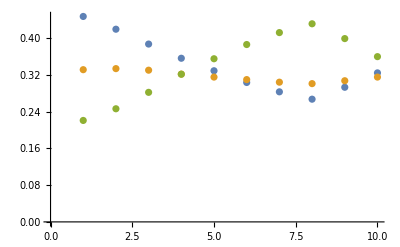

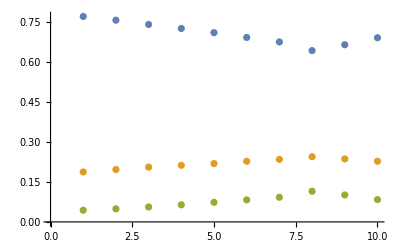

```mathematica
ListPlot[Transpose@visibilityscores]
ListPlot[Transpose@spatiotemporalscores]
```

```mathematica
visibilityscores2=Table[Module[{total,scores},
scores=ParallelTable[ImageMeasurements[ImageMultiply[visibility[[j]],i],"MeanIntensity"],{i,featurelist[[j]]}];
total=Total[scores];
If[total≠0,scores/total,scores]
],{j,n}];
```

```mathematica
spatiotemporalscores2=Table[Module[{total,scores},
scores=ParallelTable[ImageMeasurements[ImageMultiply[spatiotemporal[[j]],i],"MeanIntensity"],{i,featurelist[[j]]}];
total=Total[scores];
If[total≠0,scores/total,scores]
],{j,n}];
```

```mathematica
ListPlot[Transpose@visibilityscores2]
ListPlot[Transpose@spatiotemporalscores2]
```

-Graphics-

-Graphics-

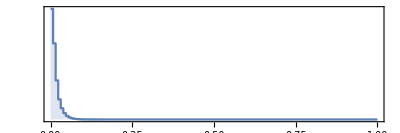

```mathematica
ImageHistogram[spatiotemporal[[1]]]
```

```mathematica
HistogramList[Flatten@ImageData[spatiotemporal[[1]]]];
```

```mathematica
Image/@Rescale/@ImageDisplacements[Rasterize/@spatio[[1;;5]]];
```

```mathematica
colorvolume[[1]];
ImageAdjust@ImageMultiply[colorvolume[[1]],ImageAdd[spatiotemporal[[1]],0.05]];
```

```mathematica
xi=ImageResize[Vortex[vortices,range,1],ImageDimensions[Vortex[vortices,range,1]]/4];
yi=ImageResize[spatiotemporal[[1]],ImageDimensions[spatiotemporal[[1]]]/4];
zi=ImageResize[visibility[[1]],ImageDimensions[visibility[[1]]]/4];
```

```mathematica
x=Flatten@ImageData@xi;
y=Flatten@ImageData@yi;
z=Flatten@ImageData@zi;
```

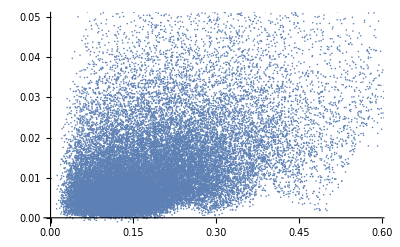

```mathematica
ListPlot[Transpose@{x,y}]
```

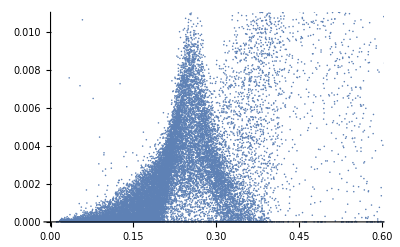

```mathematica
ListPlot[Transpose@{x,z}]
```

```mathematica
ListPointPlot3D[Transpose@{x,y,z},Axes->True,AxesLabel->Automatic]
```

yout -Graphics3D-

-Graphics3D-